# Conformal Gauss Gauge in Minkowski

## Initialisation

```mathematica
<<xAct`xTensor`;
$DefInfoQ=False;
<<xAct`xCoba`;
$CVVerbose=False;
$PrePrint =ScreenDollarIndices;
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.4, {2025,12,29}

CopyRight (C) 2003-2026, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor` version 1.3.0, {2025,12,29}

CopyRight (C) 2002-2026, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2026, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
DefManifold[M,4,{a,b,c,d,e,f,h,i,j,k,l,m,n,o,p,q,z1,z2,z3,z4,z5,z6}]
DefMetric[-1,g[-a,-b],cd,{";","∇"}]
DefCovD[wc[-a],{":","∇^∧ "}]
```

We will define a 4 velocity  with a unit 4 velocity  and length  along with a covector . The four acceleration will be denoted . The acceleration of the unit velocity will be given by .

```mathematica
DefParameter[s]
DefParameter[τ]
DefTensor[dΓ[a,-b,-c],{M,s,τ}]
sDerivativeSub={HoldPattern[u[indA_]PD[-indA_][Christoffelcd[indB_,-indC_,-indD_]]]:>dΓ[indB,-indC,-indD],HoldPattern[u[indA_]PD[-indA_][expr_]]:>ParamD[s][expr//ContractMetric],HoldPattern[v[indA_]PD[-indA_][expr_]]:>Χ[]^2ParamD[s][expr//ContractMetric]};
paramDtoDSub={ParamD[s][x_]:>D[x,s],ParamD[τ][x_]:>D[x,τ]};
DefTensor[v[a],{M,s,τ}]
DefTensor[u[a],{M,s,τ}]
DefTensor[Χ[],{M,s,τ}]
DefTensor[β[-a],{M,s,τ}]
DefTensor[α[a],{M,s,τ}]
DefTensor[dα[a],{M,s,τ}]
```

Now we define the CGEs, starting from Weyl transport with .

```mathematica
DefTensor[S[-a,-b,c,d],M]
SSub=MakeRule[{S[-z1,-z2,z3,z4],delta[-z1,z4]delta[-z2,z3]+delta[-z2,z4]delta[-z1,z3]-g[-z1,-z2]g[z3,z4]}];
weyl2LeviV=MakeRule[{wc[-z1][v[z2]],cd[-z1][v[z2]]+S[-z1,-z3,z2,z4]β[-z4]v[z3]}];
CGE1WC=v[a]wc[-a][v[b]]==0
%/.weyl2LeviV
%/.SSub//ToCanonical//ContractMetric
```

v | a
  ((∇^∧)_a v | b
 )==0

v | a
  (S |   |   | b | d
a | c |   |   v | c
  β |  
d+∇_a v | b
 )==0

2 v | a
  v | b
  β |  
a-v |  
a v | a
  β | b
 +v | a
  ∇_a v | b
 ==0

Show that the second equation is conformally invariant. IS IT THE ONLY POSSIBLE CONFORMALLY INVARIANT CONDITION ON β????

```mathematica
LHS1=v[b]cd[-b][v[a]];
RHS1=-2β[-b]v[b]v[a]+v[-b]v[b]β[a];
LHS2=v[b]cd[-b][β[-a]];
RHS2=β[-b]v[b]β[-a]-1/2 β[-b]β[b]v[-a];
CGE1=LHS1==RHS1
CGE2=LHS2==RHS2
```

v | b
  ∇_b v | a
 ==v |  
b v | b
  β | a
 -2 v | a
  v | b
  β |  
b

v | b
  ∇_b β |  
a==v | b
  β |  
a β |  
b-1/2 v |  
a β |  
b β | b

## Deriving the Third Order Formulation

Now we find the form of these equations in terms of the unit 4 velocity . First we define rules for replacing  with  and .

```mathematica
uSub=MakeRule[{v[z1],Χ[]^2u[z1]},MetricOn->All,ContractMetrics->True];
vSub=MakeRule[{u[z1],Χ[]^(-2)v[z1]},MetricOn->All,ContractMetrics->True];
αDef=MakeRule[{u[z1]cd[-z1][u[z2]],α[z2]},MetricOn->All,ContractMetrics->True];
αSub=MakeRule[{α[z2],u[z1]cd[-z1][u[z2]]},MetricOn->All,ContractMetrics->True];
uRules=Join[MakeRule[{u[z1]u[-z1],1},MetricOn->All,ContractMetrics->True],MakeRule[{α[z1]u[-z1],0},MetricOn->All,ContractMetrics->True]];
CGE1/.uSub//ToCanonical
αχEqn=%/.αDef/.uRules
```

u | b
  Χ^4 ∇_b u | a
 +2 u | a
  u | b
  Χ^3 ∇_b Χ==u |  
b u | b
  β | a
  Χ^4-2 u | a
  u | b
  β |  
b Χ^4

α | a
  Χ^4+2 u | a
  u | b
  Χ^3 ∇_b Χ==β | a
  Χ^4-2 u | a
  u | b
  β |  
b Χ^4

Contracting with  gives an expression for the derivative of .

```mathematica
u[-a]*αχEqn//ToCanonical
(SameDummies[%/.uRules]/(2Χ[]^3)//ToCanonical//ContractMetric/.uRules//CovDToChristoffel)/.sDerivativeSub
ΧDotEqn=%;
```

u | a
  α |  
a Χ^4+2 u |  
a u | a
  u | b
  Χ^3 ∇_b Χ==u | a
  β |  
a Χ^4-2 u |  
a u | a
  u | b
  β |  
b Χ^4

∂_s Χ==-1/2 u | a
  β |  
a Χ

Now we substitute back into the  equation involving .

```mathematica
ΧDotSub=MakeRule[{ParamD[s][Χ[]],-(1/2)u[z1]β[-z1]Χ[]}];
((αχEqn//CovDToChristoffel)/Χ[]^4)/.sDerivativeSub/.ΧDotSub//ToCanonical//Simplify
αβEqn=%;
```

α | a
 +u | a
  u | b
  β |  
b==β | a

Now we substitute this expression into the second CGE equation. It makes sense to start from the second CGE equation as it describes the evolution of the covector, which essentially tells us the acceleration. We use the second CGE equation to eliminate ∇β terms and use the above expression to turn β terms into  terms.

```mathematica
cdβSub=MakeRule[{cd[-z3][β[-z1]],cd[-z3][α[-z1]+u[-z1]u[z2]β[-z2]]}];
CGE2Sub=MakeRule[{u[z1]cd[-z1][β[-z2]],u[z1]β[-z1]β[-z2]-(1/2)β[z1]β[-z1]u[-z2]},MetricOn->All,ContractMetrics->True];
αβcontraction=MakeRule[{α[-z1]β[z1],α[-z1](α[z1]+u[z1]u[z2]β[-z2])},MetricOn->All,ContractMetrics->True];
CGE2
(%/.uSub)/Χ[]^2//ToCanonical
%/.cdβSub//ToCanonical
SameDummies[(%/.CGE2Sub//ToCanonical)/.uRules]/.αDef//Simplify
%/.αβcontraction//ToCanonical
%/.uRules/.MakeRule[{u[z3]β[-z3]α[-z1],u[z3]β[-z3](β[-z1]-u[-z1]u[z2]β[-z2])}]
CGE3=(g[a,c]%//ToCanonical//Simplify)
```

v | b
  ∇_b β |  
a==v | b
  β |  
a β |  
b-1/2 v |  
a β |  
b β | b

u | b
  ∇_b β |  
a==u | b
  β |  
a β |  
b-1/2 u |  
a β |  
b β | b

u |  
a u | b
  β | c
  ∇_b u |  
c+u | b
  ∇_b α |  
a+u | b
  u | c
  β |  
b ∇_c u |  
a+u |  
a u | b
  u | c
  ∇_c β |  
b==u | b
  β |  
a β |  
b-1/2 u |  
a β |  
b β | b

u |  
a α |  
b β | b
 +u | b
  (α |  
a β |  
b+u |  
a u | c
  β |  
b β |  
c+∇_b α |  
a)==u | b
  β |  
a β |  
b

u |  
a α |  
b α | b
 +u | b
  α |  
a β |  
b+u |  
a u | b
  u | c
  α |  
b β |  
c+u |  
a u | b
  u | c
  β |  
b β |  
c+u | b
  ∇_b α |  
a==u | b
  β |  
a β |  
b

u |  
a α |  
b α | b
 +u |  
a u | b
  u | c
  β |  
b β |  
c+u | c
  (β |  
a-u |  
a u | b
  β |  
b) β |  
c+u | b
  ∇_b α |  
a==u | b
  β |  
a β |  
b

u | c
  α |  
b α | b
 +u | a
  ∇_a α | c
 ==0

We must also derive an equation for the length χ of the 4 velocity, otherwise we cannot properly integrate to obtain the curve. To remove the covector from the  equation, we must differentiate again. The key final step is replacing β_a β^a with a form where each β is replaced with βSubstitution.

```mathematica
ΧDotEqn
u[c]cd[-c][%[[1]]]==u[c]cd[-c][%[[2]]]//ToCanonical
(%/.CGE2Sub/.αDef//ToCanonical//CovDToChristoffel)/.sDerivativeSub/.ΧDotSub/.uRules
(%/.MakeRule[{β[-z1]β[z1],(α[-z1]+u[-z1]u[z2]β[-z2])(α[z1]+u[z1]u[z3]β[-z3])}]//ToCanonical)/.uRules
ddΧEqn=(%/.MakeRule[{α[z1]β[-z1],α[z1](α[-z1]+u[-z1]u[z2]β[-z2])}]//ToCanonical)/.uRules
```

∂_s Χ==-1/2 u | a
  β |  
a Χ

u | a
  ∇_a ∂_s Χ==-1/2 u | a
  β | c
  Χ ∇_a u |  
c-1/2 u | a
  u | c
  Χ ∇_c β |  
a-1/2 u | a
  u | c
  β |  
a ∇_c Χ

∂_s ∂_s Χ==-1/2 α | a
  β |  
a Χ+1/4 u | a
  u | b
  β |  
a β |  
b Χ-1/2 u | a
  u | c
  β |  
a β |  
c Χ+1/4 β |  
c β | c
  Χ

∂_s ∂_s Χ==1/4 α |  
a α | a
  Χ-1/2 α | a
  β |  
a Χ

∂_s ∂_s Χ==-1/4 α |  
a α | a
  Χ

## Solving The Vacuum Radial Case

First we construct the framework for turning our tensor equations into component equations.

```mathematica
DefChart[mink,M,{0,1,2,3},{x0[],x1[],x2[],x3[]}];

coordSub={x0[]->t[s],x1[]->r[s],x2[]->θ0,x3[]->ϕ0};
MetricInBasis[g,-mink,DiagonalMatrix[{1,-1,-x1[]^2,-x1[]^2Sin[x2[]]^2}]];
MetricCompute[g,mink,All];

gddC=ToCTensor[g,{-mink,-mink}]/.TensorValues[g]/.coordSub;
guuC=ToCTensor[g,{mink,mink}]/.TensorValues[g]/.coordSub;
ΓuddC=ToCTensor[ChristoffelcdPDmink,{mink,-mink,-mink}]/.TensorValues[ChristoffelcdPDmink]/.coordSub;

ToCTensor[ChristoffelcdPDmink,{mink,-mink,-mink}]/.TensorValues[ChristoffelcdPDmink]/.coordSub;
dΓuddC=Head[ParamD[s][%[a,-b,-c]]/.paramDtoDSub];

tensorSub=Flatten[{
MakeRule[{g[-z1,-z2],gddC[-z1,-z2]}],
MakeRule[{g[z1,z2],guuC[z1,z2]}],
MakeRule[{Christoffelcd[z1,-z2,-z3],ΓuddC[z1,-z2,-z3]},MetricOn->All],
MakeRule[{dΓ[z1,-z2,-z3],dΓuddC[z1,-z2,-z3]},MetricOn->All],
MakeRule[{u[z1],CTensor[{u0[s],u1[s],0,0},{mink}][z1]},MetricOn->All],
MakeRule[{ParamD[s][u[z1]],CTensor[{u0'[s],u1'[s],0,0},{mink}][z1]},MetricOn->All],
MakeRule[{ParamD[s,s][u[z1]],CTensor[{u0''[s],u1''[s],0,0},{mink}][z1]},MetricOn->All],
MakeRule[{v[z1],CTensor[{v0[s],v1[s],0,0},{mink}][z1]},MetricOn->All],
MakeRule[{β[-z1],CTensor[{β0[s],β1[s],β2[s],β3[s]},{-mink}][-z1]},MetricOn->All],
Χ[]->χ[s],
ParamD[s][Χ[]]->χ'[s],
ParamD[s,s][Χ[]]->χ''[s]
}];
```

Now we define the frame version of CGE3. We handle second derivatives manually for simplicity.

```mathematica
(α[a]/.αSub//CovDToChristoffel//ToCanonical)/.sDerivativeSub;
ParamD[s][α[a]]==(u[d]PD[-d][%]//ToCanonical)/.sDerivativeSub
MakeRule[{ParamD[s][α[z1]],dΓ[z1,-z2,-z3]u[z2]u[z3]+2Christoffelcd[z1,-z2,-z3]u[z2]ParamD[s][u[z3]]+ParamD[s,s][u[z1]]}];
CGE3
(%//CovDToChristoffel//ToCanonical)/.sDerivativeSub/.αDef/.%%
ToCanonical[(%/.αSub//CovDToChristoffel)/.sDerivativeSub,UseMetricOnVBundle->None]//.sDerivativeSub
CGE3CTensor=%//.tensorSub
```

∂_s α | a
 ==dΓ | a |   |  
  | d | b u | b
  u | d
 +2 Γ[∇] | a |   |  
  | b | c u | b
  ∂_s u | c
 +∂_s ∂_s u | a

u | c
  α |  
b α | b
 +u | a
  ∇_a α | c
 ==0

dΓ | c |   |  
  | a | b u | a
  u | b
 +u | c
  α |  
a α | a
 +Γ[∇] | c |   |  
  | a | b u | a
  α | b
 +2 Γ[∇] | c |   |  
  | a | b u | a
  ∂_s u | b
 +∂_s ∂_s u | c
 ==0

dΓ | c |   |  
  | a | b u | a
  u | b
 +Γ[∇] | c |   |  
  | a | e Γ[∇] | e |   |  
  | b | d u | a
  u | b
  u | d
 -Γ[∇] | e |   |  
  | a | f Γ[∇] | f |   |  
  | b | d u | a
  u | b
  u | c
  u | d
  u |  
e+Γ[∇] | c |   |  
  | b | a u | b
  ∂_s u | a
 +u | c
  ∂_s u |  
a ∂_s u | a
 +2 Γ[∇] | c |   |  
  | a | b u | a
  ∂_s u | b
 +Γ[∇] | d |   |  
  | b | a u | a
  u | b
  u | c
  ∂_s u |  
d-Γ[∇] | a |   |  
  | b | d u |  
a u | b
  u | c
  ∂_s u | d
 +∂_s ∂_s u | c
 ==0

u0[s] u0'[s]^2-u0[s] u1'[s]^2+u0''[s]
u1[s] u0'[s]^2-u1[s] u1'[s]^2+u1''[s]
0
0 | c
 ==0

Our system of equations consists of the above 2 as well as the normalisation of u and the orthogonality relation with α.

```mathematica
CGE30=Basis[-c,{0,mink}]CGE3CTensor//ContractBasis//Simplify;
CGE31=Basis[-c,{1,mink}]CGE3CTensor//ContractBasis//Simplify;
norm=g[-a,-b]u[a]u[b]==1/.tensorSub;
orth=(g[-a,-b]α[a]u[b]==0/.αSub//CovDToChristoffel//ToCanonical)/.sDerivativeSub//.tensorSub;
usystem={CGE30,CGE31,norm,orth};
%//MatrixForm
```

(u0[s] u0'[s]^2+u0''[s]==u0[s] u1'[s]^2
u1[s] u0'[s]^2+u1''[s]==u1[s] u1'[s]^2
u0[s]^2-u1[s]^2==1
u0[s] u0'[s]-u1[s] u1'[s]==0)

Now we solve the system for u0. Note that solving the normalisation condition automatically means the orthogonality condition is satisfied.

```mathematica
Solve[usystem[[3]],u0[s]]
u1system=usystem/.%[[2]]/.D[%[[2]],s]/.D[%[[2]],{s,2}]//FullSimplify
u1system//MatrixForm
```

{{u0[s]→-√(1+u1[s]^2)},{u0[s]→√(1+u1[s]^2)}}

{(u1[s] (-u1[s] u1'[s]^2+(1+u1[s]^2) u1''[s]))/(√(1+u1[s]^2))==0,u1''[s]==(u1[s] u1'[s]^2)/(1+u1[s]^2),True,True}

((u1[s] (-u1[s] u1'[s]^2+(1+u1[s]^2) u1''[s]))/(√(1+u1[s]^2))==0
u1''[s]==(u1[s] u1'[s]^2)/(1+u1[s]^2)
True
True)

Now we use the remaining equations to solve for u1.

```mathematica
DSolve[u1system[[2]],u1[s],s]//Flatten
(Solve[usystem[[3]]/.%,u0[s]]//Simplify)/.Sqrt[Cosh[x_]^2]:>Cosh[x]
Join[%[[2]],%%]
uSol=Join[%,D[%,s],D[%,{s,2}]]/.{C[1]->Subscript[C, 1],C[2]->Subscript[C, 2]};
```

Attributes::notfound: Symbol DSolveDispatchODE not found.

{u1[s]→Sinh[C[1] (s+C[2])]}

{{u0[s]→-Cosh[C[1] (s+C[2])]},{u0[s]→Cosh[C[1] (s+C[2])]}}

{u0[s]→Cosh[C[1] (s+C[2])],u1[s]→Sinh[C[1] (s+C[2])]}

So far we have two free constants. These correspond to the angle of the initial velocity in the t-r plane and an initial covector value. We don’t get two values for the initial covector because we know it must satisfy a condition with α and u. This restricts us to two degrees of freedom.

Now we solve the χ equation. We solve for an initially normalised v^a, that is, χ[0]=1. It’s also handy to work with the initial derivative of χ, so we define this here too.

```mathematica
ddΧEqn
(%/.αSub//CovDToChristoffel//Expand)//.sDerivativeSub//.tensorSub
%/.uSol//Simplify
DSolve[{%,χ[0]==1},χ[s],s]//Flatten
Join[%,D[%,s],D[%,{s,2}]];
Solve[χ'[s]==dχ0/.%/.s->0,C[1]]//Flatten
dχ0Sub=Solve[C[1]==(C[1]/.%),dχ0]//Flatten
χSol=%%%/.%%//FullSimplify
```

∂_s ∂_s Χ==-1/4 α |  
a α | a
  Χ

χ''[s]==χ[s] (-1/4 u0'[s]^2+1/4 u1'[s]^2)

C_1^2 χ[s]==4 χ''[s]

Attributes::notfound: Symbol DSolveDispatchODE not found.

{χ[s]→-ⅇ^(-(s C_1)/2) (-ⅇ^(s C_1)-C[1]+ⅇ^(s C_1) C[1])}

{C[1]→(-2 dχ0+C_1)/(2 C_1)}

{dχ0→-1/2 (-1+2 C[1]) C_1}

{χ[s]→Cosh[(s C_1)/2]+(2 dχ0 Sinh[(s C_1)/2])/C_1,χ'[s]→dχ0 Cosh[(s C_1)/2]+1/2 Sinh[(s C_1)/2] C_1,χ''[s]→1/4 C_1 (2 dχ0 Sinh[(s C_1)/2]+Cosh[(s C_1)/2] C_1)}

So now we have recovered our 3 degrees of freedom. C_1,C_2 and dχ0. These correspond to initial velocity direction and 2 initial covector components.

Now we must use this solution to compute the solution for the original variables. To work out the solution for β we use the αβ relation derived above.

```mathematica
{v0[s]->χ[s]^2u0[s],v1[s]->χ[s]^2u1[s]}/.uSol/.χSol//Simplify
vSol=Join[%,D[%,s],D[%,{s,2}]];
αβEqn
(%/.αSub//CovDToChristoffel//Expand)/.sDerivativeSub//.tensorSub/.uSol;
βsystem=Table[Basis[-a,{IND,mink}]%//ContractBasis,{IND,0,3}];
%//MatrixForm
β123Sol=Solve[βsystem,{β0[s],β1[s],β2[s],β3[s]}]//Simplify//Flatten
```

{v0[s]→Cosh[C_1 (s+C_2)] (Cosh[(s C_1)/2]+(2 dχ0 Sinh[(s C_1)/2])/C_1)^2,v1[s]→Sinh[C_1 (s+C_2)] (Cosh[(s C_1)/2]+(2 dχ0 Sinh[(s C_1)/2])/C_1)^2}

α | a
 +u | a
  u | b
  β |  
b==β | a

(Sinh[C_1 (s+C_2)] C_1+Cosh[C_1 (s+C_2)]^2 β0[s]+Cosh[C_1 (s+C_2)] Sinh[C_1 (s+C_2)] β1[s]==β0[s]
Cosh[C_1 (s+C_2)] C_1+Cosh[C_1 (s+C_2)] Sinh[C_1 (s+C_2)] β0[s]+Sinh[C_1 (s+C_2)]^2 β1[s]==-β1[s]
0==-β2[s]/r[s]^2
0==-(Csc[θ0]^2 β3[s])/r[s]^2)

Solve::svars: Equations may not give solutions for all "solve" variables.

{β1[s]→-Sech[C_1 (s+C_2)] (C_1+Sinh[C_1 (s+C_2)] β0[s]),β2[s]→0,β3[s]→0}

This method above only gives β1 because if we solve the above without /.uSol, we see both β0 and β1 have a 1-u0^2-u1^2 in the denominator so we can only solve for one in terms of the other. We use the dχ equation to solve for β0.

```mathematica
ΧDotEqn
%/.tensorSub/.χSol/.uSol/.β123Sol//Simplify
Solve[%,β0[s]]//FullSimplify//Flatten
βSol=Join[%,D[%,s],D[%,{s,2}],β123Sol/.%,D[β123Sol/.%,s],D[β123Sol/.%,{s,2}]]//Simplify;
```

∂_s Χ==-1/2 u | a
  β |  
a Χ

(Sech[C_1 (s+C_2)] (-Sinh[1/2 C_1 (s+2 C_2)] C_1^2+2 dχ0 Sinh[(s C_1)/2] β0[s]+C_1 (2 dχ0 Cosh[1/2 C_1 (s+2 C_2)]+Cosh[(s C_1)/2] β0[s])))/C_1==0

{β0[s]→(C_1 (-2 dχ0 Cosh[1/2 C_1 (s+2 C_2)]+Sinh[1/2 C_1 (s+2 C_2)] C_1))/(2 dχ0 Sinh[(s C_1)/2]+Cosh[(s C_1)/2] C_1)}

Before integrating to find the position as a function of s, we check that v and β satisfy the original equations. We also do a reparameterisation. The reparameterisation is done so that τ represents the proper time along the curve.

```mathematica
Trig1={Cosh[x__+y__]:>Cosh[x]Cosh[y]+Sinh[x]Sinh[y],Sinh[x__+y__]:>Sinh[x]Cosh[y]+Cosh[x]Sinh[y]};
Trig2={Cosh[2ArcTanh[x__]]:>-(x^2+1)/(x^2-1),Sinh[2ArcTanh[x__]]:>-(2x)/(x^2-1)};
τ2s=DSolve[{τ'[s]==χ[s]^-2/.χSol//FullSimplify,τ[0]==0}/.%,τ[s],s]/.τ[s]->τ//FullSimplify//Flatten
s2τ=Solve[%/.Rule->Equal,s]/.C[1]->0//Simplify//Flatten
```

Attributes::notfound: Symbol DSolveDispatchODE not found.

{τ→1/(dχ0+1/2 Coth[(s C_1)/2] C_1)}

{s→(2 ArcCoth[(2-2 dχ0 τ)/(τ C_1)])/C_1}

Now we check the original CGEs are satisfied. Mathematica finds it easier if we first find a new solution in terms of τ, rather than substitute τ in all at once. The τSol function just does a bunch of algebra.

```mathematica
τSol[x_]:=x->(x/.vSol/.χSol/.βSol/.s2τ//FullSimplify)/.dχ0+Subscript[C, 1]/2->TEMP/.Trig1/.TEMP->dχ0+Subscript[C, 1]/2/.Trig1/.Trig2//Simplify
Solτ={τSol[χ[s]],τSol[χ'[s]],τSol[v0[s]],τSol[v0'[s]],τSol[v1[s]],τSol[v1'[s]],τSol[β0[s]],τSol[β0'[s]],τSol[β1[s]],τSol[β1'[s]],β2[s]->(β2[s]/.βSol),β3[s]->(β3[s]/.βSol),β2'[s]->(β2'[s]/.βSol),β3'[s]->(β3'[s]/.βSol)}
CGE1
(%//CovDToChristoffel//Expand)/.sDerivativeSub//.tensorSub/.paramDtoDSub;
Table[Basis[-a,{IND,mink}]%//ContractBasis,{IND,0,3}]
%/.Solτ//FullSimplify
CGE2
(%//CovDToChristoffel//Expand)/.sDerivativeSub//.tensorSub/.paramDtoDSub;
Table[Basis[{IND,-mink},a]%//ContractBasis,{IND,0,3}]
%/.Solτ//FullSimplify
```

{χ[s]→-2/((-1+dχ0 τ) √(4-(τ^2 C_1^2)/(-1+dχ0 τ)^2)),χ'[s]→(4 dχ0 (-1+dχ0 τ)-τ C_1^2)/(2 (-1+dχ0 τ) √(4-(τ^2 C_1^2)/(-1+dχ0 τ)^2)),v0[s]→(4 (4 (-1+dχ0 τ)^2 Cosh[C_1 C_2]-4 τ (-1+dχ0 τ) Sinh[C_1 C_2] C_1+τ^2 Cosh[C_1 C_2] C_1^2))/((-4 (-1+dχ0 τ)^2+τ^2 C_1^2)^2),v0'[s]→1/((-4 (-1+dχ0 τ)^2+τ^2 C_1^2)^2)2 (-16 dχ0 (-1+dχ0 τ)^3 Cosh[C_1 C_2]+8 (-1+dχ0 τ)^2 (1+2 dχ0 τ) Sinh[C_1 C_2] C_1-12 τ (-1+dχ0 τ) Cosh[C_1 C_2] C_1^2-2 τ^2 (-3+2 dχ0 τ) Sinh[C_1 C_2] C_1^3+τ^3 Cosh[C_1 C_2] C_1^4),v1[s]→(4 (4 (-1+dχ0 τ)^2 Sinh[C_1 C_2]-4 τ (-1+dχ0 τ) Cosh[C_1 C_2] C_1+τ^2 Sinh[C_1 C_2] C_1^2))/((-4 (-1+dχ0 τ)^2+τ^2 C_1^2)^2),v1'[s]→1/((-4 (-1+dχ0 τ)^2+τ^2 C_1^2)^2)2 (-16 dχ0 (-1+dχ0 τ)^3 Sinh[C_1 C_2]+8 (-1+dχ0 τ)^2 (1+2 dχ0 τ) Cosh[C_1 C_2] C_1-12 τ (-1+dχ0 τ) Sinh[C_1 C_2] C_1^2-2 τ^2 (-3+2 dχ0 τ) Cosh[C_1 C_2] C_1^3+τ^3 Sinh[C_1 C_2] C_1^4),β0[s]→(1-2 dχ0 τ) Sinh[C_1 C_2] C_1+1/2 Cosh[C_1 C_2] (4 dχ0 (-1+dχ0 τ)+τ C_1^2),β0'[s]→1/8 (4 (-1+dχ0 τ)^2-τ^2 C_1^2) (-4 dχ0 Sinh[C_1 C_2] C_1+Cosh[C_1 C_2] (4 dχ0^2+C_1^2)),β1[s]→1/4 ⅇ^(-C_1 C_2) (-ⅇ^(2 C_1 C_2) (-2 dχ0+C_1) (2-2 dχ0 τ+τ C_1)+(2 dχ0+C_1) (-2+2 dχ0 τ+τ C_1)),β1'[s]→-1/8 (4 (-1+dχ0 τ)^2-τ^2 C_1^2) (-4 dχ0 Cosh[C_1 C_2] C_1+Sinh[C_1 C_2] (4 dχ0^2+C_1^2)),β2[s]→0,β3[s]→0,β2'[s]→0,β3'[s]→0}

v | b
  ∇_b v | a
 ==v |  
b v | b
  β | a
 -2 v | a
  v | b
  β |  
b

{χ[s]^2 v0'[s]==-v0[s]^2 β0[s]-v1[s]^2 β0[s]-2 v0[s] v1[s] β1[s],χ[s]^2 v1'[s]==-2 v0[s] v1[s] β0[s]-v0[s]^2 β1[s]-v1[s]^2 β1[s],0==-(v0[s]^2 β2[s])/r[s]^2+(v1[s]^2 β2[s])/r[s]^2,0==-(Csc[θ0]^2 v0[s]^2 β3[s])/r[s]^2+(Csc[θ0]^2 v1[s]^2 β3[s])/r[s]^2}

{True,True,True,True}

v | b
  ∇_b β |  
a==v | b
  β |  
a β |  
b-1/2 v |  
a β |  
b β | b

{χ[s]^2 β0'[s]==1/2 v0[s] β0[s]^2+v1[s] β0[s] β1[s]+1/2 v0[s] β1[s]^2+(v0[s] β2[s]^2)/(2 r[s]^2)+(Csc[θ0]^2 v0[s] β3[s]^2)/(2 r[s]^2),χ[s]^2 β1'[s]==1/2 v1[s] β0[s]^2+v0[s] β0[s] β1[s]+1/2 v1[s] β1[s]^2-(v1[s] β2[s]^2)/(2 r[s]^2)-(Csc[θ0]^2 v1[s] β3[s]^2)/(2 r[s]^2),-(v1[s] β2[s])/r[s]+χ[s]^2 β2'[s]==v0[s] β0[s] β2[s]+v1[s] β1[s] β2[s],-(v1[s] β3[s])/r[s]+χ[s]^2 β3'[s]==v0[s] β0[s] β3[s]+v1[s] β1[s] β3[s]}

{True,True,True,True}

Now we need to integrate the velocity vector to obtain the coordinates of the conformal geodesics.

```mathematica
Table[Basis[-a,{IND,mink}]v[a]/.tensorSub/.Solτ//ContractBasis,{IND,0,1}]//FullSimplify;
{γt'[τ]==%[[1]],γr'[τ]==%[[2]]};
DSolve[%,{γt[τ],γr[τ]},τ]//Flatten
Solve[(γt[τ]/.%/.τ->0)==t0,C[1]]//Flatten
Solve[(γr[τ]/.%%/.τ->0)==r0,C[2]]//Flatten
γSol=%%%/.%%/.%/.{γt[τ]->t[s],γr[τ]->r[s]}//FullSimplify;
```

Attributes::notfound: Symbol DSolveDispatchODE not found.

{γt[τ]→C[1]+(ⅇ^(-C_1 C_2) (-8 dχ0 (1+ⅇ^(2 C_1 C_2)) (-1+dχ0 τ)+4 (-1+ⅇ^(2 C_1 C_2)) (-1+2 dχ0 τ) C_1-2 (1+ⅇ^(2 C_1 C_2)) τ C_1^2))/((4 dχ0^2-C_1^2) (4 (-1+dχ0 τ)^2-τ^2 C_1^2)),γr[τ]→C[2]+(ⅇ^(-C_1 C_2) (-8 dχ0 (-1+ⅇ^(2 C_1 C_2)) (-1+dχ0 τ)+4 (1+ⅇ^(2 C_1 C_2)) (-1+2 dχ0 τ) C_1-2 (-1+ⅇ^(2 C_1 C_2)) τ C_1^2))/((4 dχ0^2-C_1^2) (4 (-1+dχ0 τ)^2-τ^2 C_1^2))}

{C[1]→-(ⅇ^(-C_1 C_2) (-2 dχ0-2 dχ0 ⅇ^(2 C_1 C_2)+4 dχ0^2 ⅇ^(C_1 C_2) t0-C_1+ⅇ^(2 C_1 C_2) C_1-ⅇ^(C_1 C_2) t0 C_1^2))/(-4 dχ0^2+C_1^2)}

{C[2]→-(ⅇ^(-C_1 C_2) (2 dχ0-2 dχ0 ⅇ^(2 C_1 C_2)+4 dχ0^2 ⅇ^(C_1 C_2) r0+C_1+ⅇ^(2 C_1 C_2) C_1-ⅇ^(C_1 C_2) r0 C_1^2))/(-4 dχ0^2+C_1^2)}

Now we find expressions for our integration constants in terms of the initial covector and radial velocity.  Note that C_2 has two solutions, only one of which is real. We will still mainly work in terms of the original constants but will use these expressions to choose initial conditions later.

```mathematica
(v1[s]/.Solτ/.τ->0)==dr0//FullSimplify//Flatten
{Sinh[Subscript[C, 1] Subscript[C, 2]]->dr0,Cosh[Subscript[C, 1] Subscript[C, 2]]->Sqrt[1+dr0^2]};
(β0[s]/.Solτ/.τ->0)==β00/.%//FullSimplify
((β1[s]/.Solτ/.τ->0)==β10//FullSimplify)/.%%
Solve[{%,%%},{Subscript[C, 1],dχ0}]//Flatten
Solve[%%%%%/.%,Subscript[C, 2]][[2]]/.C[1]->0
switchConstants=Join[%%,%];
```

dr0==Sinh[C_1 C_2]

2 √(1+dr0^2) dχ0+β00==dr0 C_1

β10+√(1+dr0^2) C_1==2 dr0 dχ0

{C_1→-dr0 β00-√(1+dr0^2) β10,dχ0→1/2 (-√(1+dr0^2) β00-dr0 β10)}

{C_2→ArcSinh[dr0]/(-dr0 β00-√(1+dr0^2) β10)}

## Dragging Coordinates

Now we drag the coordinates using  and . Since the coordinates are scalars we can use any connection.

```mathematica
τDerivativeSub=ParamD[s][TENS_]:>χ[s]^-2D[TENS,τ];
{v[a]cd[-a][T[τ]]==1,v[a]cd[-a][R[τ]]==0,v[a]cd[-a][Θ[τ]]==0,v[a]cd[-a][Φ[τ]]==0}
(%//CovDToChristoffel)/.sDerivativeSub/.τDerivativeSub/.tensorSub
DSolve[{%,T[0]==t0,R[0]==r0,Θ[0]==θ0,Φ[0]==ϕ0},{T[τ],R[τ],Θ[τ],Φ[τ]},τ]//Flatten
{t[s],r[s],θ0,ϕ0}/.γSol
NewToOld=Table[D[%,{τ,r0,θ0,ϕ0}[[IND]]],{IND,1,4}]//Simplify;
OldToNew=Inverse[%]//Simplify//MatrixForm
```

{v | a
  ∇_a T[τ]==1,v | a
  ∇_a R[τ]==0,v | a
  ∇_a Θ[τ]==0,v | a
  ∇_a Φ[τ]==0}

{T'[τ]==1,R'[τ]==0,Θ'[τ]==0,Φ'[τ]==0}

Attributes::notfound: Symbol DSolveDispatchODE not found.

General::stop: Further output of Attributes::notfound will be suppressed during this calculation.

{T[τ]→t0+τ,R[τ]→r0,Θ[τ]→θ0,Φ[τ]→ϕ0}

{(4 (-1+dχ0 τ) (t0 (-1+dχ0 τ)-τ Cosh[C_1 C_2])+τ^2 C_1 (2 Sinh[C_1 C_2]-t0 C_1))/(4 (-1+dχ0 τ)^2-τ^2 C_1^2),r0-(ⅇ^(-C_1 C_2) τ)/(2-2 dχ0 τ+τ C_1)-(ⅇ^(C_1 C_2) τ)/(-2+2 dχ0 τ+τ C_1),θ0,ϕ0}

(((-4 (-1+dχ0 τ)^2+τ^2 C_1^2)^2)/(4 (4 (-1+dχ0 τ)^2 Cosh[C_1 C_2]-4 τ (-1+dχ0 τ) Sinh[C_1 C_2] C_1+τ^2 Cosh[C_1 C_2] C_1^2)) | (ⅇ^(-C_1 C_2) (-4 (-1+ⅇ^(2 C_1 C_2)) (-1+dχ0 τ)^2+4 (1+ⅇ^(2 C_1 C_2)) τ (-1+dχ0 τ) C_1-(-1+ⅇ^(2 C_1 C_2)) τ^2 C_1^2))/(2 (4 (-1+dχ0 τ)^2 Cosh[C_1 C_2]-4 τ (-1+dχ0 τ) Sinh[C_1 C_2] C_1+τ^2 Cosh[C_1 C_2] C_1^2)) | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

## Weyl Transporting Frame

We define a generic vector F^a to make substitutions later then substitute the true basis vectors in later.

```mathematica
DefTensor[F[a],{M,s,τ}]
weyl2LeviF=MakeRule[{wc[-z1][F[z2]],cd[-z1][F[z2]]+S[-z1,-z3,z2,z4] β[-z4]F[z3]},MetricOn->All,ContractMetrics->True];
v[a]wc[-a][F[b]]
(%/.weyl2LeviF//CovDToChristoffel//Expand)
%/.sDerivativeSub/.SSub//ToCanonical
%/.MakeRule[{F[z1],CTensor[{F0[τ],F1[τ],F2[τ],F3[τ]},{mink}][z1]}];
frameSystem=%//.tensorSub/.τDerivativeSub;
```

** MakeRule: Potential problems moving indices on the LHS.

v | a
  ((∇^∧)_a F | b
 )

Γ[∇] | b |   |  
  | a | c F | c
  v | a
 +F | c
  S |   |   | b | d
a | c |   |   v | a
  β |  
d+v | a
  ∂_a F | b

Γ[∇] | b |   |  
  | a | c F | a
  v | c
 +F | b
  v | a
  β |  
a+F | a
  v | b
  β |  
a-F | a
  g |   |  
a | c v | c
  β | b
 +Χ^2 ∂_s F | b

Solving the first system should give us back v^a. Note the constants of integration C[2] and C[3] introduced here are different for all of the frame components and different to the C[2] which appears above. We need to be careful when substituting initial conditions. This time vector computation is just to check our method. We already know it should be v^a. On the last line we substract the solutions to check we are right.

```mathematica
Table[Basis[-b,{A,mink}]frameSystem//ContractBasis,{A,0,3}]/.Solτ/.γSol//Simplify
DSolve[{%[[1]]==0,%[[2]]==0},{F0[τ],F1[τ]},τ]//Flatten//Simplify
DSolve[%%[[3]]==0,F2[τ],τ]//Flatten//Simplify
DSolve[%%%[[4]]==0,F3[τ],τ]//Flatten//Simplify
FSol=Join[%%%,%%,%];
e0C1=Solve[(F0[τ]/.FSol)==(v0[s]/.Solτ)/.τ->0,C[1]]//Flatten//Simplify
e0C2=Solve[(F1[τ]/.FSol)==(v1[s]/.Solτ)/.τ->0,C[2]]//Flatten//Simplify
{F0[τ]==v0[s],F1[τ]==v1[s]}/.FSol/.Solτ/.%/.%%//Simplify
```

{(-4 F1[τ] C_1+F0[τ] (8 dχ0 (-1+dχ0 τ)-2 τ C_1^2)+(4 (-1+dχ0 τ)^2-τ^2 C_1^2) F0'[τ])/(4 (-1+dχ0 τ)^2-τ^2 C_1^2),(-4 F0[τ] C_1+F1[τ] (8 dχ0 (-1+dχ0 τ)-2 τ C_1^2)+(4 (-1+dχ0 τ)^2-τ^2 C_1^2) F1'[τ])/(4 (-1+dχ0 τ)^2-τ^2 C_1^2),(F2[τ] (8 dχ0 r0 (-1+dχ0 τ)+(4-8 dχ0 τ) Sinh[C_1 C_2]+4 τ Cosh[C_1 C_2] C_1-2 r0 τ C_1^2))/(4 (-1+dχ0 τ) (r0 (-1+dχ0 τ)-τ Sinh[C_1 C_2])+2 τ^2 Cosh[C_1 C_2] C_1-r0 τ^2 C_1^2)+F2'[τ],(F3[τ] (8 dχ0 r0 (-1+dχ0 τ)+(4-8 dχ0 τ) Sinh[C_1 C_2]+4 τ Cosh[C_1 C_2] C_1-2 r0 τ C_1^2))/(4 (-1+dχ0 τ) (r0 (-1+dχ0 τ)-τ Sinh[C_1 C_2])+2 τ^2 Cosh[C_1 C_2] C_1-r0 τ^2 C_1^2)+F3'[τ]}

{F0[τ]→-((-4 dχ0^2+C_1^2)^2 (4 (-1+dχ0 τ) (C[1]+dχ0 τ C[1]+τ C[2])-τ^2 C[1] C_1^2))/(4 (-4 (-1+dχ0 τ)^2+τ^2 C_1^2)^2),F1[τ]→((-4 dχ0^2+C_1^2)^2 (4 (-1+dχ0 τ)^2 (2 dχ0 C[1]+C[2])+τ ((4-2 dχ0 τ) C[1]+τ C[2]) C_1^2))/(4 C_1 (2-2 dχ0 τ+τ C_1)^2 (-2+2 dχ0 τ+τ C_1)^2)}

Attributes::notfound: Symbol DSolveDispatchODE not found.

{F2[τ]→C[1]/(4 (-1+dχ0 τ) (r0 (-1+dχ0 τ)-τ Sinh[C_1 C_2])+2 τ^2 Cosh[C_1 C_2] C_1-r0 τ^2 C_1^2)}

Attributes::notfound: Symbol DSolveDispatchODE not found.

{F3[τ]→C[1]/(4 (-1+dχ0 τ) (r0 (-1+dχ0 τ)-τ Sinh[C_1 C_2])+2 τ^2 Cosh[C_1 C_2] C_1-r0 τ^2 C_1^2)}

{C[1]→(16 Cosh[C_1 C_2])/((-4 dχ0^2+C_1^2)^2)}

{C[2]→-(2 (16 dχ0^5 C[1]-8 Sinh[C_1 C_2] C_1-8 dχ0^3 C[1] C_1^2+dχ0 C[1] C_1^4))/((-4 dχ0^2+C_1^2)^2)}

{True,True}

We now define some functions for substituting frame components into the equations.

```mathematica
F2e0={F0[τ]->e00[τ],F1[τ]->e01[τ],F2[τ]->e02[τ],F3[τ]->e03[τ]};
F2e1={F0[τ]->e10[τ],F1[τ]->e11[τ],F2[τ]->e12[τ],F3[τ]->e13[τ]};
F2e2={F0[τ]->e20[τ],F1[τ]->e21[τ],F2[τ]->e22[τ],F3[τ]->e23[τ]};
F2e3={F0[τ]->e30[τ],F1[τ]->e31[τ],F2[τ]->e32[τ],F3[τ]->e33[τ]};
e0Sol=Join[{FSol[[1]],FSol[[2]]}/.e0C2/.e0C1,{FSol[[3]],FSol[[4]]}/.C[1]->0]/.F2e0//Simplify;
e1Sol=(FSol/.F2e1);
e2Sol=(FSol/.F2e2);
e3Sol=(FSol/.F2e3);
```

Now we require that the initial frame be orthogonal and radial. That is, e_0 and e_1 are orthonormal and e_2 and e_3 only have components in the θ and ϕ directions initially.

```mathematica
e10[τ]e10[τ]-e11[τ]e11[τ]==-1/.e1Sol/.τ->0//FullSimplify
e00[τ]e10[τ]-e01[τ]e11[τ]==0/.e0Sol/.e1Sol/.τ->0//FullSimplify
Solve[{%,%%},{C[1],C[2]}]//Simplify
e1SolRad1={e1Sol[[1]]/.%[[1]],e1Sol[[2]]/.%[[1]],e1Sol[[3]]/.C[1]->0,e1Sol[[4]]/.C[1]->0}//Simplify;
e1SolRad2={e1Sol[[1]]/.%%[[2]],e1Sol[[2]]/.%%[[2]],e1Sol[[3]]/.C[1]->0,e1Sol[[4]]/.C[1]->0}//Simplify;
```

1/256 (C[1]^2-(2 dχ0 C[1]+C[2])^2/C_1^2) (-4 dχ0^2+C_1^2)^4==-1

((-((2 dχ0 C[1]+C[2]) Sinh[C_1 C_2])+C[1] Cosh[C_1 C_2] C_1) (-4 dχ0^2+C_1^2))/C_1==0

{{C[1]→-(16 Sinh[C_1 C_2])/(√((-4 dχ0^2+C_1^2)^4)),C[2]→(32 dχ0 Sinh[C_1 C_2]-16 Cosh[C_1 C_2] C_1)/(√((-4 dχ0^2+C_1^2)^4))},{C[1]→(16 Sinh[C_1 C_2])/(√((-4 dχ0^2+C_1^2)^4)),C[2]→(-32 dχ0 Sinh[C_1 C_2]+16 Cosh[C_1 C_2] C_1)/(√((-4 dχ0^2+C_1^2)^4))}}

Now the initial angular basis vectors, for which the only calculation is the normalisation.

```mathematica
{e2Sol[[1]]/.C[1]->0/.C[2]->0,e2Sol[[2]]/.C[1]->0/.C[2]->0,e2Sol[[3]],e2Sol[[4]]/.C[1]->0}
-r0^2 e22[τ]^2==-1/.%/.τ->0
Solve[%,C[1]]
e2SolRad1={e2Sol[[1]]/.C[1]->0/.C[2]->0,e2Sol[[2]]/.C[1]->0/.C[2]->0,e2Sol[[3]]/.%[[1]],e2Sol[[4]]/.C[1]->0};
e2SolRad2={e2Sol[[1]]/.C[1]->0/.C[2]->0,e2Sol[[2]]/.C[1]->0/.C[2]->0,e2Sol[[3]]/.%%[[2]],e2Sol[[4]]/.C[1]->0};
```

{e20[τ]→0,e21[τ]→0,e22[τ]→C[1]/(4 (-1+dχ0 τ) (r0 (-1+dχ0 τ)-τ Sinh[C_1 C_2])+2 τ^2 Cosh[C_1 C_2] C_1-r0 τ^2 C_1^2),e23[τ]→0}

-C[1]^2/16==-1

{{C[1]→-4},{C[1]→4}}

```mathematica
{e3Sol[[1]]/.C[1]->0/.C[2]->0,e3Sol[[2]]/.C[1]->0/.C[2]->0,e3Sol[[3]]/.C[1]->0,e3Sol[[4]]}
-r0^2 Sin[θ0]^2e33[τ]^2==-1/.%/.τ->0
Solve[%,C[1]]
e3SolRad1={e3Sol[[1]]/.C[1]->0/.C[2]->0,e3Sol[[2]]/.C[1]->0/.C[2]->0,e3Sol[[3]]/.C[1]->0,e3Sol[[4]]/.%[[1]]};
e3SolRad2={e3Sol[[1]]/.C[1]->0/.C[2]->0,e3Sol[[2]]/.C[1]->0/.C[2]->0,e3Sol[[3]]/.C[1]->0,e3Sol[[4]]/.%%[[2]]};
```

{e30[τ]→0,e31[τ]→0,e32[τ]→0,e33[τ]→C[1]/(4 (-1+dχ0 τ) (r0 (-1+dχ0 τ)-τ Sinh[C_1 C_2])+2 τ^2 Cosh[C_1 C_2] C_1-r0 τ^2 C_1^2)}

-1/16 C[1]^2 Sin[θ0]^2==-1

{{C[1]→-4 Csc[θ0]},{C[1]→4 Csc[θ0]}}

Now we should be able to construct a full solution and find an equation for the conformal factor. We define a matrix of frame components as a CTensor in which the index structure is e_â^μ.

```mathematica
{{e00[τ],e01[τ],e02[τ],e03[τ]},{e10[τ],e11[τ],e12[τ],e13[τ]},{e20[τ],e21[τ],e22[τ],e23[τ]},{e30[τ],e31[τ],e32[τ],e33[τ]}};
%//MatrixForm
e=CTensor[%%,{-mink,mink}];
eInv=CTensor[Inverse[%%%],{-mink,-mink}]//Simplify;
g[-a,-b]e[-c,a]e[-d,b]/.tensorSub/.Solτ/.γSol/.e0Sol/.e1SolRad1/.e2SolRad1/.e3SolRad1//Simplify
ΩSol=Ω[τ]->1/Sqrt[%Basis[{0,-mink},c]Basis[{0,-mink},d]//ContractBasis]
Ω[τ]^2%%/.ΩSol//Simplify
```

(e00[τ] | e01[τ] | e02[τ] | e03[τ]
e10[τ] | e11[τ] | e12[τ] | e13[τ]
e20[τ] | e21[τ] | e22[τ] | e23[τ]
e30[τ] | e31[τ] | e32[τ] | e33[τ])

16/((-4 (-1+dχ0 τ)^2+τ^2 C_1^2)^2) | 0 | 0 | 0
0 | -16/((-4 (-1+dχ0 τ)^2+τ^2 C_1^2)^2) | 0 | 0
0 | 0 | -16/((-4 (-1+dχ0 τ)^2+τ^2 C_1^2)^2) | 0
0 | 0 | 0 | -16/((-4 (-1+dχ0 τ)^2+τ^2 C_1^2)^2) |   |  
c | d

Ω[τ]→1/(4 √(1/((-4 (-1+dχ0 τ)^2+τ^2 C_1^2)^2)))

1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1 |   |  
c | d

So we see that we do in fact have the conformal factor such that . Now we check that the third derivative is indeed 0.

```mathematica
Ω[τ]==(Ω[τ]/.ΩSol)
D[%,{τ,3}]//Simplify
```

Ω[τ]==1/(4 √(1/((-4 (-1+dχ0 τ)^2+τ^2 C_1^2)^2)))

Ω^(3)[τ]==0

## Choosing an Initial Surface

We define an initial surface G(t_0,r_0)=0. The the normal vector to the surface is ∇G and we want the initial v to be proportional to this. It’s easier now to work in terms of the set of dr0, and initial β values. Note the -ve sign on the spatial components of dG. We want e_0^a = ∇^a G=η^ab∇_b G.

```mathematica
{D[G[t0,r0],t0],-D[G[t0,r0],r0],0,0};
dG=%/(%[[1]]^2-%[[2]]^2)
e0Sol/.switchConstants//FullSimplify
e01[τ]==dG[[2]]/.%/.τ->0//Simplify
dr0Sub=Solve[%,dr0]//Flatten;
```

{(G^(1,0)[t0,r0])/(-(G^(0,1)[t0,r0])^2+(G^(1,0)[t0,r0])^2),-(G^(0,1)[t0,r0])/(-(G^(0,1)[t0,r0])^2+(G^(1,0)[t0,r0])^2),0,0}

{e00[τ]→(4 (√(1+dr0^2) β00^2 τ^2+2 β00 τ (2+dr0 β10 τ)+√(1+dr0^2) (4+β10^2 τ^2)))/((4+τ (4 √(1+dr0^2) β00+β00^2 τ+β10 (4 dr0-β10 τ)))^2),e01[τ]→(-8 β10 τ (2+√(1+dr0^2) β00 τ)+4 dr0 (4-(β00^2+β10^2) τ^2))/((4+τ (4 √(1+dr0^2) β00+β00^2 τ+β10 (4 dr0-β10 τ)))^2),e02[τ]→0,e03[τ]→0}

dr0==(G^(0,1)[t0,r0])/((G^(0,1)[t0,r0])^2-(G^(1,0)[t0,r0])^2)

If we didn’t insist that our initial frame be hypersurface orthogonal then we would be free to choose dr0 as we desire. Now we define a function that generates replacement rules for specific initial surfaces.

```mathematica
initialSurface[S_]:={G[t0,r0]->S,D[G[t0,r0],t0]->D[S,t0],D[G[t0,r0],r0]->D[S,r0]};
```

#### Constant Time Initial Surface

{t0+(2 τ (2 √(1+dr0^2)+β00 τ))/(4+τ (4 √(1+dr0^2) β00+β00^2 τ+β10 (4 dr0-β10 τ))),(4 r0+4 √(1+dr0^2) r0 β00 τ+4 dr0 (1+r0 β10) τ+(-2 β10+r0 (β00-β10) (β00+β10)) τ^2)/(4+τ (4 √(1+dr0^2) β00+β00^2 τ+β10 (4 dr0-β10 τ)))}

{t0+(2 τ (2+β00 τ))/(4+τ (4 β00+β00^2 τ-β10^2 τ)),(4 r0+4 r0 β00 τ+(-2 β10+r0 (β00-β10) (β00+β10)) τ^2)/(4+τ (4 β00+β00^2 τ-β10^2 τ))}

{(2 (2-τ) τ)/(4-4 τ),(4 r0-4 r0 τ-2 τ^2)/(4-4 τ)}

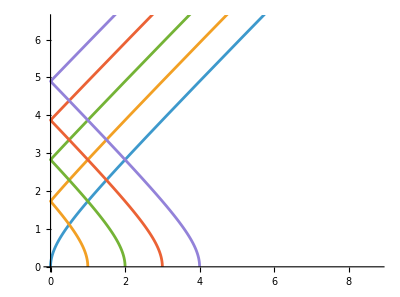

```mathematica
{t[s],r[s]}/.γSol/.switchConstants//FullSimplify
%/.dr0Sub/.initialSurface[t0]
%/.β00->-1/.β10->1/.t0->0
{{Abs[%[[2]]],%[[1]]}/.r0->0,{Abs[%[[2]]],%[[1]]}/.r0->1,{Abs[%[[2]]],%[[1]]}/.r0->2,{Abs[%[[2]]],%[[1]]}/.r0->3,{Abs[%[[2]]],%[[1]]}/.r0->4};
ParametricPlot[%,{τ,0,1}]
```

#### Linear Initial Surface

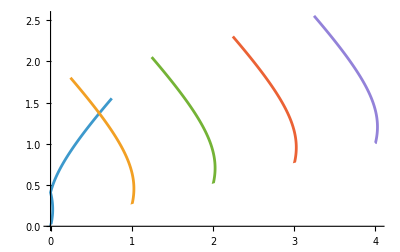

```mathematica
{t[s],r[s]}/.γSol/.switchConstants//FullSimplify;
surf=t0-r0/4;
%%/.dr0Sub/.initialSurface[surf];
%/.β00->1/.β10->1;
{Abs[%[[2]]],%[[1]]}/.Solve[surf==0,t0];
{%/.r0->0,%/.r0->1,%/.r0->2,%/.r0->3,%/.r0->4};
geodesics=ParametricPlot[%,{τ,0,3}];
hypersurface=Plot[τ/4,{τ,0,4},PlotStyle->{White}];
Show[geodesics,hypersurface]
```

### A Third Case: Sqrt[r0]

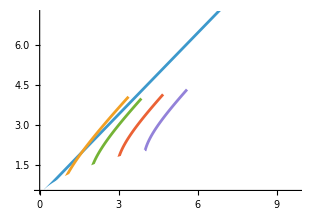

```mathematica
{t[s],r[s]}/.γSol/.switchConstants//FullSimplify;
surf=t0-Sqrt[r0+0.1];
%%/.dr0Sub/.initialSurface[surf]//Simplify;
%/.β00->1/.β10->-1;
{Abs[%[[2]]],%[[1]]}/.Solve[surf==0,t0]//Simplify;
{%/.r0->0.2,%/.r0->1,%/.r0->2,%/.r0->3,%/.r0->4};
geodesics=ParametricPlot[%,{τ,0,3}];
hypersurface=Plot[Sqrt[τ+0.1],{τ,0,4},PlotStyle->{White}];
Show[geodesics,hypersurface]
```